# Pokrytí dat RBF sítí Demonstrace pokrytí vstupních dat složitější RBF sítí.

## Načtení knihovny NeuralNetworks

Nejdříve načteme knihovnu neuronových sítí.

```mathematica
<< NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm]
```

## Příprava trénovacích dat

Pokrytí dat budeme předvádět na klasifikaci do dvou tříd. Data budeme mít jednoduchá dvoudimenzionální, každá třída dat se skládá ze třech dobře oddělených, shluků. Shluky se vzájemně nepřekrývají.
Vygenerujeme tyto data.

```mathematica
values=10;
cluster1x =RandomReal[{7,6},{values,1}];cluster1y=RandomReal[ {11,12},{values,1}];
cluster2x =RandomReal[{-4,-5},{values,1}];cluster2y=RandomReal[ {9,10},{values,1}];
cluster3x =RandomReal[{0,-1},{values,1}];cluster3y=RandomReal[ {12,13},{values,1}];
cluster1=Join[cluster1x,cluster1y,2];
cluster2=Join[cluster2x,cluster2y,2];
cluster3=Join[cluster3x,cluster3y,2];
inDataClass1 = Join[cluster1,cluster2,cluster3];
cluster4x =RandomReal[{2,1},{values,1}];cluster4y=RandomReal[ {4,5},{values,1}];
cluster5x =RandomReal[{-3,-4},{values,1}];cluster5y=RandomReal[ {12,13},{values,1}];
cluster6x =RandomReal[{9,8},{values,1}];cluster6y=RandomReal[ {10,9},{values,1}];
cluster4=Join[cluster4x,cluster4y,2];
cluster5=Join[cluster5x,cluster5y,2];
cluster6=Join[cluster6x,cluster6y,2];
inDataClass2 = Join[cluster4,cluster5,cluster6];
inData= Join[inDataClass1,inDataClass2];
outClass1=ConstantArray[{1,0},{3*values}];outClass2 = ConstantArray[{0,1},{3*values}];
outData= Join[outClass1,outClass2];
```

Takto vypadají naše vynerovaná vstupní data. Můžeme je chápat jako seznam bodů, které jsou určeny svými {x,y} souřadnicemi.

```mathematica
inData
```

{{6.09305,11.8132},{6.08882,11.1465},{6.24748,11.4061},{6.4512,11.7608},{6.35629,11.1704},{6.37529,11.9733},{6.08354,11.5269},{6.92344,11.2778},{6.94817,11.8879},{6.465,11.5921},{-4.85576,9.78066},{-4.8447,9.45709},{-4.50194,9.20006},{-4.41895,9.42151},{-4.21074,9.95823},{-4.10521,9.30417},{-4.13911,9.45002},{-4.16674,9.47274},{-4.63543,9.92325},{-4.48022,9.74843},{-0.186096,12.1163},{-0.44659,12.7088},{-0.664057,12.8692},{-0.440129,12.6206},{-0.644414,12.6319},{-0.809105,12.123},{-0.821842,12.0088},{-0.0575208,12.1311},{-0.477054,12.267},{-0.842949,12.0722},{1.95657,4.2786},{1.55194,4.8242},{1.80061,4.00091},{1.19902,4.01707},{1.27858,4.92508},{1.51624,4.88021},{1.81124,4.38663},{1.81715,4.63761},{1.5389,4.31164},{1.36687,4.85189},{-3.26649,12.1088},{-3.70612,12.5069},{-3.8456,12.4318},{-3.51679,12.8694},{-3.75367,12.1107},{-3.06967,12.3616},{-3.13895,12.588},{-3.4223,12.5284},{-3.3886,12.0256},{-3.91354,12.9044},{8.78282,9.29243},{8.39319,9.12217},{8.22161,9.292},{8.54465,9.78244},{8.17701,9.05209},{8.55624,9.92466},{8.62159,9.27615},{8.71108,9.21172},{8.95759,9.33928},{8.15176,9.86883}}

A takto vypadají data výstupní.

```mathematica
outData
```

{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}

Vygenerovaná data si můžeme pro lepší představu zobrazit. Každá třída dat je v grafu zobrazena jinou barvou.

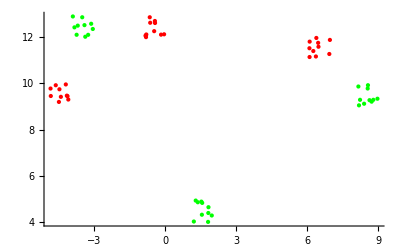

```mathematica
ListPlot[{inDataClass1,inDataClass2},PlotStyle->{Red,Green}]
```

Po vygenerování dat můžeme začít učit síť.

## Učení RBF sítě

Tato jednoduchá data budeme chtít klasifikovat pomocí RBF sítě se třemi RBF neurony, dvěma vstupy a dvěma výstupními neurony.
Vytvoříme RBF síť podle popisu výše.

```mathematica
net=InitializeRBFNet[inData,outData,3,LinearPart->False,OutputNonlinearity->Sigmoid]
```

RBFNet[{{w1, λ, w2}},{Neuron → Exp, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 3, 21, 22, 30, 19.8413866}, OutputNonlinearity → Sigmoid, NumberOfInputs → 2}]

Zobrazíme si informace o sítí. Tím se ujistíme že síť je opravdu taková jakou jsme popsali.

```mathematica
NetInformation[net]
```

Radial Basis Function network. Created 2011-3-21 at 22:30. The network has 2 inputs and 2 outputs.  It consists of 3 basis functions of Exp type. There is a nonlinearity at the output of type Sigmoid.

Naučíme vytvořenou síť na našich datech.

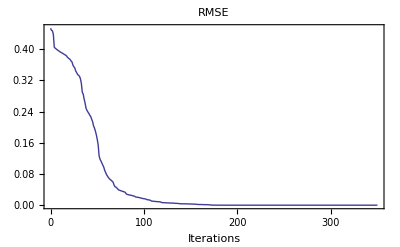

```mathematica
{net2,record}=NeuralFit[net,inData,outData,350,ReportFrequency->20];
```

## Výstup neuronové sítě

Podívejme se jak neuronová síť pokrývá jednotlivé třídy dat. Nejprve si zobrazíme výstup pro červenou třídu. Oblast grafu ohraničená červenou čarou určuje oblast dat, kterou neuronová síť klasifikuje do červené třídy. Tato oblast odpovídá datům, pro které první výstupní neuron vrací hodnotu větší než 0.5.

```mathematica
out1=Plot3D[net2[{x,y}][[1]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.2]];
inDataClass13d2=inDataClass1/.{x_?NumberQ,y_?NumberQ}:>{x,y,0};
inDataClass23d2=inDataClass2/.{x_?NumberQ,y_?NumberQ}:>{x,y,0};
data3d2=ListPointPlot3D[{inDataClass13d2,inDataClass23d2},PlotStyle->{{PointSize[Large],Red},{PointSize[Large],Green}},PlotStyle->PointSize[Large]];
out1true=Plot3D[net2[{x,y}][[1]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.7], RegionFunction->Function[{x,y,z},z>0.5],BoundaryStyle->Directive[Red,Thick]];
Show[out1,out1true,data3d2]
```

-Graphics3D-

Obdobně si zobrazíme výstup pro zelenou třídu. Oblast grafu ohraničená zelenou čarou určuje oblast dat, kterou neuronová síť klasifikuje do zelené třídy. Tato oblast odpovídá datům, pro které první výstupní neuron vrací hodnotu větší než 0.5.

```mathematica
out2true=Plot3D[net2[{x,y}][[2]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.7], RegionFunction->Function[{x,y,z},z>0.5],BoundaryStyle->Directive[Green,Thick],Mesh->None];
out2=Plot3D[net2[{x,y}][[2]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.2]];
Show[out2true,out2,data3d2]
```

-Graphics3D-

Obdobný výstup klasifikace pomocí neuronové sítě. Do 2D jsou promítnuty hraniční přímky. Po ukázání na hraniční přímku se ukáže výstup sítě ve formě vzorce.

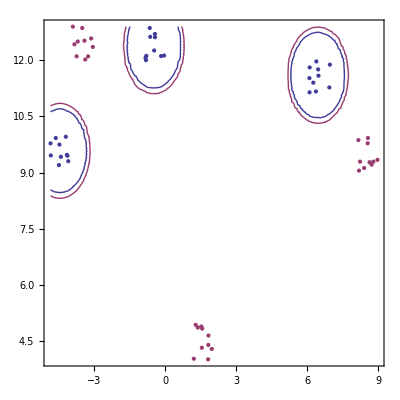

```mathematica
NetPlot[net2,inData,outData, DataFormat->Classifier]
```

## Výstup RBF neuronů

Nyní se podíváme na “vnitřnosti” neuronové sítě. Nejprve si zobrazíme výstup všech tří RBF neuronů. Abychom se dostali k výstupu RBF neuronů musíme upravit strukturu sítě obdobně jako u ukázkového příkladu sítě s jedním neuronem. Připojíme tedy každý RBF neuron přímo na výstupní neuron s vahou 1. Na výstupních neuronech se tedy zobrazí přímo výstupy z RBF neuronů.
Provedeme popsanou úpravu.

```mathematica
net3=net2;(*nechceme si rozbít původní síť*)
net3[[1,1,3]]=Append[IdentityMatrix[3],{0,0,0}];(*nastaveni vystupni vrstvy*)
```

A zobrazíme výstup RBF neuronů.

```mathematica
gauss1=Plot3D[net3[{x,y}][[1]],{x,-10,10},{y,0,25},PlotRange->All];
gauss2=Plot3D[net3[{x,y}][[2]],{x,-10,10},{y,0,25},PlotRange->All];
gauss3=Plot3D[net3[{x,y}][[3]],{x,-10,10},{y,0,25},PlotRange->All];
Show[gauss1,gauss2,gauss3]
```

-Graphics3D-

Výstup může mít více podob, je závislý na tom jak se neuronová síť naučila data. Pokud vidíte pouze jednu gaussovu funkci, je možné, že ostatní jsou “pod” ní. Následující průhůedné zobrazení to objasní.

Přidáme do grafu ještě vstupní data pro lepší představu o jejich pokrytí (levé tlačítko myši otáčí grafem).

```mathematica
inDataClass13d=inDataClass1/.{x_?NumberQ,y_?NumberQ}:>{x,y,0.50};
inDataClass23d=inDataClass2/.{x_?NumberQ,y_?NumberQ}:>{x,y,0.50};
gauss0O=Plot3D[net3[{x,y}][[1]],{x,-10,10},{y,0,25},PlotRange->All,PlotStyle->Opacity[0.4]];
gauss1O=Plot3D[net3[{x,y}][[2]],{x,-10,10},{y,0,25},PlotRange->All,PlotStyle->Opacity[0.4]];
gauss2O=Plot3D[net3[{x,y}][[3]],{x,-10,10},{y,0,25},PlotRange->All,PlotStyle->Opacity[0.4]];
data3d=ListPointPlot3D[{inDataClass13d,inDataClass23d},PlotStyle->{{PointSize[Large],Red},{PointSize[Large],Green}},PlotStyle->PointSize[Large]];
Show[gauss0O,gauss1O,gauss2O,data3d]
```

-Graphics3D-